```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
```

```mathematica
Decreasing of residue(n is number of nodes);
```

```mathematica
(*triangle 1*)
```

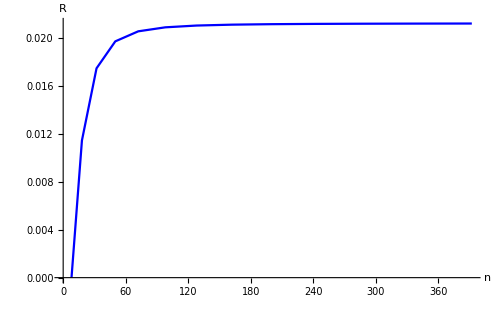

```mathematica
residueT1 =  {{8,2.22*10^-16},{18,0.0114367},{32,0.0174472},{50,0.0196944},{72,0.02053},{98,0.0208636},{128,0.0210121},{162,0.0210858},{200,0.021126},{242,0.0211496},{288,0.0211642},{338,0.0211737},{392,0.0211801}};
gr1=ListLinePlot[residueT1,
GridLines->Full,
ImageSize->500,
PlotStyle->{Blue},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

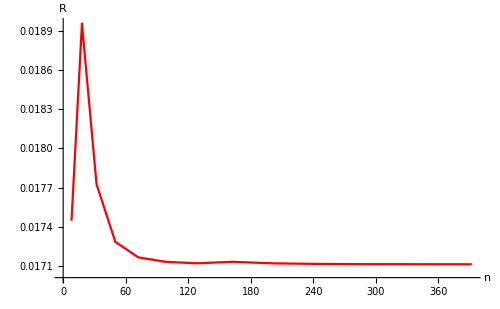

```mathematica
(*triangle 2*)
residueT2= {{8,0.0174472},{18,0.0189541},{32,0.0177267},{50,0.0172864},{72,0.0171679},{98,0.0171339},{128,0.0171224},{162,0.0171339},{200,0.0171224},{242,0.0171179},{288,0.0171159},{392,0.017115}};
gr2=ListLinePlot[residueT2,
GridLines->Full,
ImageSize->500,
PlotStyle->{Red},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

```mathematica
(*rectangle 1*)
```

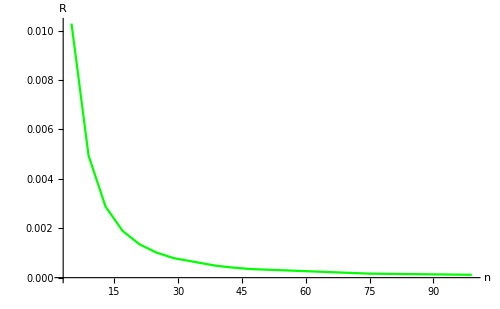

```mathematica
residueR1 =  {{9,9.41*10^-15},{16, 7.45*10^-15},{25,4.07*10^-14},{36,3.86*10^-14},{49,5.84*10^-14},{64,1.3*10^-14},{81,1.2*10^-13},{100,1.21*10^-13},{121,1.31*10^-13},{144,1.8*10^-13},{169,1.8*10^-13},{196,1.8*10^-13},{400,5.06404*10^-13}};
gr3=ListLinePlot[residueR1,
GridLines->Full,
ImageSize->500,
PlotStyle->{Green},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

```mathematica
(*rectangle 2*)
```

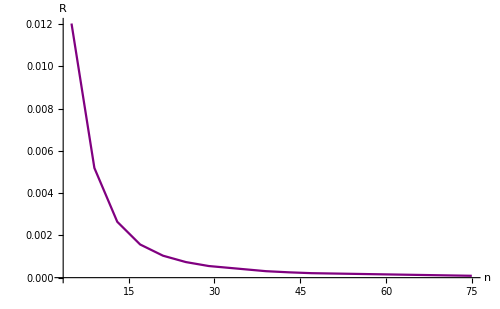

```mathematica
residueR2=  {{4,1.19732},{9, 0.249047},{16,0.288585},{25,0.148413},{36,0.0868982},{49,0.0552596},{64,0.0373004},{81,0.0263593},{100,0.0193099},{121,0.0145698},{144,0.011259},{324,1.83755*10^-12}};
gr4=ListLinePlot[residueR2,
GridLines->Full,
ImageSize->500,
PlotStyle->{Purple},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

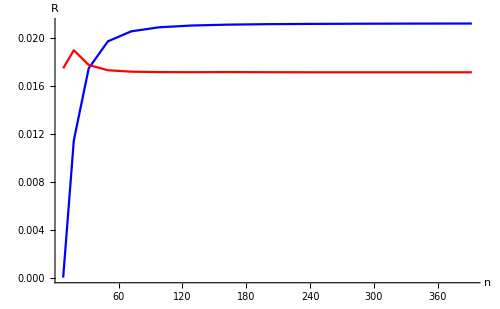

```mathematica
Show[gr1,gr2,PlotRange->All]
```

```mathematica
Decreasing of residue(n is number of finite elements);
```

```mathematica
Print["Triangles 1",Solve[(n-1)(n-1)*2==18.0,n]]
Print["Triangles 2",Solve[(n-1)/2(n-1)/2*2==18.0,n]]
Print["Rectangles 1",Solve[(n-1)(n-1)==16.0,n]]
Print["Rectangles 2",Solve[(n-1)/2(n-1)/2==16.0,n]]
```

Triangles 1{{n→-2.},{n→4.}}

Triangles 2{{n→-5.},{n→7.}}

Rectangles 1{{n→-3.},{n→5.}}

Rectangles 2{{n→-7.},{n→9.}}